# Electric field vector plots

In earlier analysis of test results during “the Spain Trip” it was seen that the inductance for high separations was far too low, or even negative, relative to experimental values. This notebook will attempt to determine if those results were valid or a programming error.

There are two parts to this. First, the magnitude of inductance in side wires needs to be analysed. Second, the magnitude of inductance of wires perpendicular to each other must be determined to see if they are of sufficiently high value to be included in the calculations.

## Rectangular vector plot of LW derived field

```mathematica
PlotRectangularEField[
svgFilePath_,
staticCoeff_,
dynamicCoeff_,
arrowScale_:0.085,
arrowHeadSize_:0.031,
numArrowsPerSide_:12,
centerSize_:0.38] := Module[
{
(* local functions *)
emf,arrowForCoordinate,rowOfArrows,allArrows,accelProduct,

(* local variables *)
graphic,arrows,r,rLen,position,xCoord,yCoord,fieldVec, arrow,front,back,accel,rDist,rUnitVec,staticEmf,dynamicEmf,totalEmf
},

emf[r_] := (
accel = {1,0,0};
rUnitVec =Normalize[r];
rDist=Norm[r];
staticEmf= Dot[rUnitVec, accel]rUnitVec/rDist;
dynamicEmf=-accel/rDist;
totalEmf=staticCoeff staticEmf +dynamicCoeff dynamicEmf;
totalEmf
);

arrowForCoordinate[x_,y_] := (
r = {x,y};
rLen = Norm[r];
If[
rLen <centerSize,
Nothing,
(
fieldVec = emf[{x,y, 0}][[1;;2]];
arrow = {arrowScale fieldVec[[1]], arrowScale fieldVec[[2]]};
front = r+ 0.5 arrow;
back = r-0.5 arrow;
{
Thickness[0.0050],
Arrowheads[arrowHeadSize Norm[fieldVec]],
Arrow[{back,front}]
}
)
]
);

rowOfArrows[x_] := (
Map[
arrowForCoordinate[x,#1]&,
Subdivide[-1,1, numArrowsPerSide]
]
);

allArrows[] :=
Map[
rowOfArrows[#1]&,
Subdivide[-1,1, numArrowsPerSide]
];

graphic = Graphics[
Join[allArrows[],{Black,Disk[{0,0},0.025]}],
ImageSize->Large
];

If[!DirectoryQ[DirectoryName[svgFilePath]],
CreateDirectory[DirectoryName[svgFilePath]]
];

Export[svgFilePath, graphic];
graphic
];
```

### Vector plot for the full acceleration term

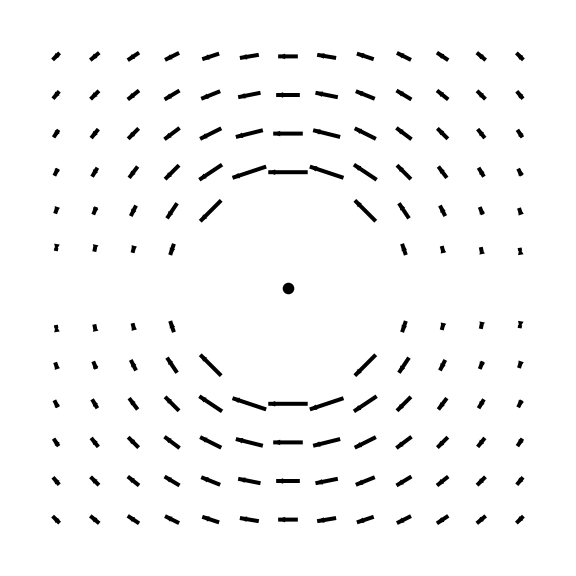

```mathematica
PlotRectangularEField[
FileNameJoin[{NotebookDirectory[],"Images","fullTermField.svg"}],
 1,
 1]
```

### Vector plot for the static acceleration term

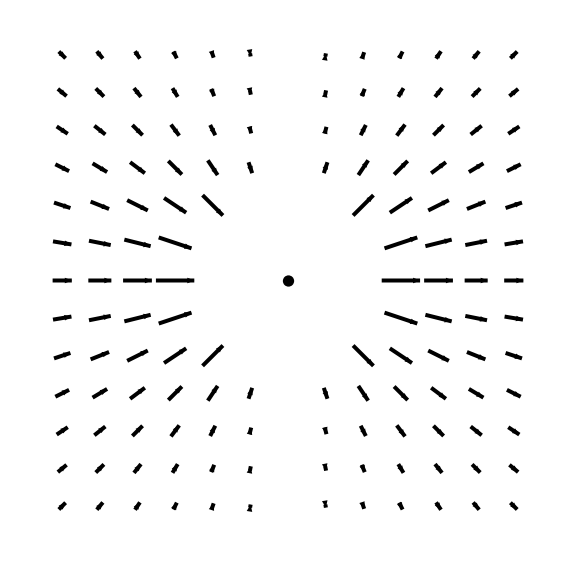

```mathematica
PlotRectangularEField[
FileNameJoin[{NotebookDirectory[],"Images","staticTermField.svg"}],
1,
0]
```

### Vector plot for the dynamic acceleration term

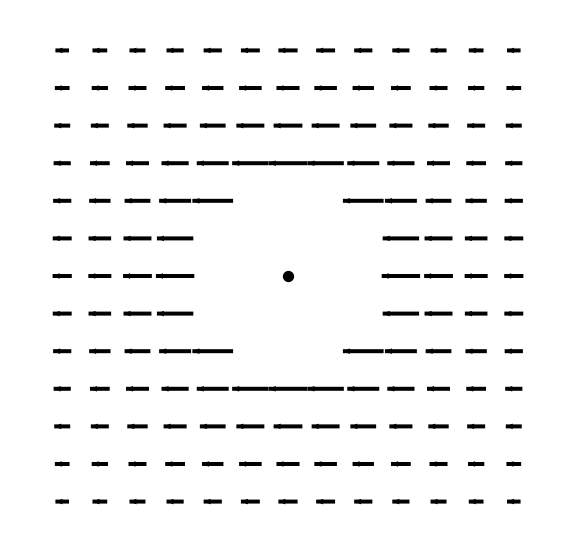

```mathematica
PlotRectangularEField[
FileNameJoin[{NotebookDirectory[],"Images","dynamicTermField.svg"}],
0,
1]
```